# Wolfram Language Basics

```mathematica
https://www.wolfram.com/wolfram-u/courses/wolfram-language/wolfram-language-basics-wl901/
```

## Calculate

WolframAlphaQueryParseResults



WolframAlphaQueryParseResults

TimeSeries[…]

WolframAlphaQueryParseResults

250000

WolframAlphaQueryNoResults

## Import, Visualize and Process Data

```mathematica
img = Import["http://www.nasa.gov/images/content/507898main_PIA04866-full_full.jpg"]
```

-Graphics-

```mathematica
ColorNegate[img]
```

-Graphics-

## Screen and Filter Data

## Doing Calculations

```mathematica
25!
```

15511210043330985984000000

## Natural Language Understanding

```mathematica
{{"[◼]", "NthDigit"}}[Pi, {1, 500}]
```

[π,{1,500}]

WolframAlphaQueryParseResults

GeoPosition[{223/4,2257/60}]

WolframAlphaQueryParseResults

benzoic acid

WolframAlphaQueryParseResults

{59500510 people,21710000 people,7990000 people,36894216 people,25575254 people,104303132 people,46026629 people,34746468 people,8671518 people,71854202 people,38312224 people,94023567 people,58160000 people,65683722 people,78659903 people,44567475 people,27462297 people,43746323 people,24706321 people,6301350 people,5626722 people,37327378 people,95793065 people,23390000 people,35712111 people,81100000 people,13245000 people,21813334 people,3180000 people,45966239 people,54426891 people}

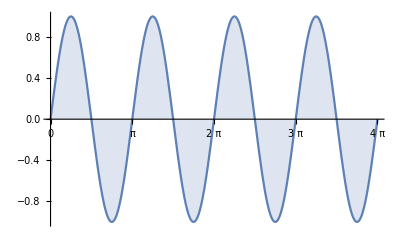

```mathematica
Plot[Sin[2x],{x, 0, 4 Pi},
Filling->Axis,
Ticks->{Range[0, 4 Pi, Pi/2], Automatic},
GridLines->{Range[0, 4 Pi, Pi/2], Automatic}]
```

## Built-in Functions

```mathematica
Expand[(x + y)^ 2]
```

x^2+2 x y+y^2

```mathematica
N[Pi, 50]
```

3.1415926535897932384626433832795028841971693993751

```mathematica
RandomReal[]
```

0.0539783

```mathematica
DateString[]
```

Sat 1 Apr 2023 15:36:50

## Arithmetic

```mathematica
2 3
```

6

```mathematica
FullForm[x + y]
```

Plus[x,y]

```mathematica
FullForm[2 x]
```

Times[2,x]

## Lists

```mathematica
{1, 2, 3}
```

{1,2,3}

```mathematica
FullForm[{1, 2, 3}]
```

List[1,2,3]

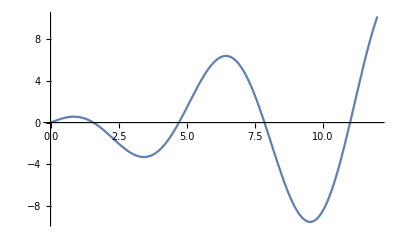

```mathematica
Plot[x Cos[x],{x, 0, 12}]
```

```mathematica
FindMinimum[x Cos[x],{x, 2}]
```

{-3.28837,{x→3.42562}}

```mathematica
Do[Print[k ^2], {k, 1, 5}]
```

1

4

9

16

25

```mathematica
Table[k^2, {k, 1, 5}]
```

{1,4,9,16,25}

```mathematica
{2, 3, 4} + {10, 20, 30}
```

{12,23,34}

```mathematica
MatrixForm[{{a, b},{c, d}}]
```

(a | b
c | d)

```mathematica
Inverse[%]
```

{{d/(-b c+a d),-b/(-b c+a d)},{-c/(-b c+a d),a/(-b c+a d)}}

```mathematica
x = 5
```

5

```mathematica
x y
```

5 y

```mathematica
xy
```

xy

```mathematica
?x
```

```mathematica
x=7
```

7

```mathematica
?x
```

```mathematica
Clear[x]
```

```mathematica
x
```

x

```mathematica
?x
```

```mathematica
Clear[x]
```

```mathematica
?x
```

## Defining Functions

```mathematica
f[x_]:= x Cos[x]
```

```mathematica
?f
```

```mathematica
f[6] // N
```

5.76102

```mathematica
Clear[f]
```

## Working with Lists

```mathematica
vec = Range[1, 28, 3]
```

{1,4,7,10,13,16,19,22,25,28}

```mathematica
Part[vec, 3]
```

7

```mathematica
Part[vec, -1]
```

28

```mathematica
Part[vec, Range[5]]
```

{1,4,7,10,13}

```mathematica
vec[[3]]
```

7

```mathematica
1;2;5
```

5

```mathematica
Part[vec, 1 ;; 5]
```

{1,4,7,10,13}

```mathematica
Take[vec, 5]
```

{1,4,7,10,13}

```mathematica
vec[[{1, 3}]]
```

{1,7}

```mathematica
vec[[;;5]]
```

{1,4,7,10,13}

```mathematica
vec[[5;;]]
```

{13,16,19,22,25,28}

```mathematica
?Plot
```

```mathematica
Information[Plot]
```

```mathematica
?Intege*
```

```mathematica
IntegerDigits[100]
```

{1,0,0}